# Ejercicio : Maquina de Turing

Estudiante : Andrey Arguedas Espinoza - 2020426569

## Código

-Graphics-

Definimos las reglas

```mathematica
rules={
{0,"0"}-> {1,"B",1},
{0,"1"}-> {4,"B",1},
{1,"0"}-> {1,"0",1},
{1,"1"}-> {1,"1",1},
{1,"B"}-> {2,"B",-1},
{2,"0"}-> {3,"B",-1},
{3,"0"}-> {3,"0",-1},
{3,"1"}-> {3,"1",-1},
{3,"B"}-> {0,"B",1},
{4,"0"}-> {4,"0",1},
{4,"1"}-> {4,"1",1},
{4,"B"}-> {5,"B",-1},
{5,"1"}-> {6,"B",-1},
{6,"0"}-> {6,"0",-1},
{6,"1"}-> {6,"1",-1},
{6,"B"}-> {0,"B",1}
};
```

Comenzamos a correr las máquinas de Turing y a graficar

```mathematica
evolution=TuringMachine[rules,{0,{{"1","1","B"},0}},4]
```

{{{0,1,0},{1,1,B}},{{4,2,1},{B,1,B}},{{4,3,2},{B,1,B}},{{5,2,1},{B,1,B}},{{6,1,0},{B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

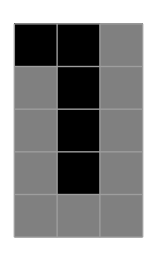

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"0","0","B"},0}},4]
```

{{{0,1,0},{0,0,B}},{{1,2,1},{B,0,B}},{{1,3,2},{B,0,B}},{{2,2,1},{B,0,B}},{{3,1,0},{B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

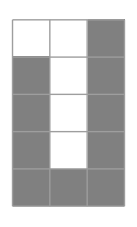

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"0","0","0","0","B"},0}},15]
```

{{{0,1,0},{0,0,0,0,B}},{{1,2,1},{B,0,0,0,B}},{{1,3,2},{B,0,0,0,B}},{{1,4,3},{B,0,0,0,B}},{{1,5,4},{B,0,0,0,B}},{{2,4,3},{B,0,0,0,B}},{{3,3,2},{B,0,0,B,B}},{{3,2,1},{B,0,0,B,B}},{{3,1,0},{B,0,0,B,B}},{{0,2,1},{B,0,0,B,B}},{{1,3,2},{B,B,0,B,B}},{{1,4,3},{B,B,0,B,B}},{{2,3,2},{B,B,0,B,B}},{{3,2,1},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

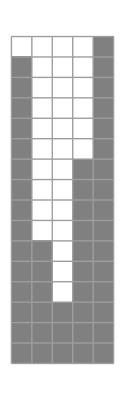

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"1","1","1","1","B"},0}},16]
```

{{{0,1,0},{1,1,1,1,B}},{{4,2,1},{B,1,1,1,B}},{{4,3,2},{B,1,1,1,B}},{{4,4,3},{B,1,1,1,B}},{{4,5,4},{B,1,1,1,B}},{{5,4,3},{B,1,1,1,B}},{{6,3,2},{B,1,1,B,B}},{{6,2,1},{B,1,1,B,B}},{{6,1,0},{B,1,1,B,B}},{{0,2,1},{B,1,1,B,B}},{{4,3,2},{B,B,1,B,B}},{{4,4,3},{B,B,1,B,B}},{{5,3,2},{B,B,1,B,B}},{{6,2,1},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

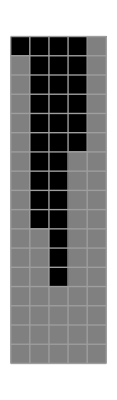

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"0","1","0","0","1","0","B"},0}},28]
```

{{{0,1,0},{0,1,0,0,1,0,B}},{{1,2,1},{B,1,0,0,1,0,B}},{{1,3,2},{B,1,0,0,1,0,B}},{{1,4,3},{B,1,0,0,1,0,B}},{{1,5,4},{B,1,0,0,1,0,B}},{{1,6,5},{B,1,0,0,1,0,B}},{{1,7,6},{B,1,0,0,1,0,B}},{{2,6,5},{B,1,0,0,1,0,B}},{{3,5,4},{B,1,0,0,1,B,B}},{{3,4,3},{B,1,0,0,1,B,B}},{{3,3,2},{B,1,0,0,1,B,B}},{{3,2,1},{B,1,0,0,1,B,B}},{{3,1,0},{B,1,0,0,1,B,B}},{{0,2,1},{B,1,0,0,1,B,B}},{{4,3,2},{B,B,0,0,1,B,B}},{{4,4,3},{B,B,0,0,1,B,B}},{{4,5,4},{B,B,0,0,1,B,B}},{{4,6,5},{B,B,0,0,1,B,B}},{{5,5,4},{B,B,0,0,1,B,B}},{{6,4,3},{B,B,0,0,B,B,B}},{{6,3,2},{B,B,0,0,B,B,B}},{{6,2,1},{B,B,0,0,B,B,B}},{{0,3,2},{B,B,0,0,B,B,B}},{{1,4,3},{B,B,B,0,B,B,B}},{{1,5,4},{B,B,B,0,B,B,B}},{{2,4,3},{B,B,B,0,B,B,B}},{{3,3,2},{B,B,B,B,B,B,B}},{{0,4,3},{B,B,B,B,B,B,B}},{{0,4,3},{B,B,B,B,B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

-Graphics-